```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/more_sectors/deq_3loop_bubble_bubble

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Reverse[{1,1,1,1,1,0,0,0,0}]
FromDigits[%,2]
```

{0,0,0,0,1,1,1,1,1}

31

### Preliminaries: start basis

```mathematica
family = topoA;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2,k3},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
(*intfam  = {-m2+sp[k1,k1],-m2+sp[k2,k2],-m2+sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],-m2+sp[k3,k3]-2 sp[k3,p]+sp[p,p],sp[k1,k1]-2 sp[k1,k2]+sp[k2,k2],sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3],sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3]}*)
```

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2,k3},Directory->"famA"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];*)

(*Save to disk*)
(*DiskSave[family];*)
```

```mathematica
(*Get["./famA/famA"];*)
```

```mathematica
(*MIs[family]*)
```

```mathematica
(*MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];*)
```

```mathematica
(*LiteRed Masters*)
(*todiff= MIs[family];*)
```

```mathematica
(*(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;*)
```

### Start From d = 2

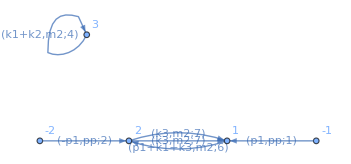

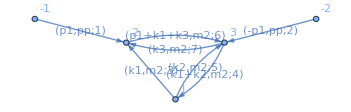

```mathematica
Import["./graphs/all/topoA_3_011.dot"]; (* triple tadpole*)
Import["./graphs/all/topoA_4_015.dot"];(*tadpole * tadpole2loop *)
Import["./graphs/all/topoA_4_027.dot"] (*tadpole * sunrise 2 loop, elliptic, 2 masters *)
Import["./graphs/all/topoA_4_030.dot"]; (* 3 loop banana, K3, 3 masters *)
Import["./graphs/all/topoA_5_031.dot"]  (* top sector, elliptic 3 masters *)
```

```mathematica
Reverse[IntegerDigits[11,2]]
Reverse[IntegerDigits[15,2]]
Reverse[IntegerDigits[27,2]]
Reverse[IntegerDigits[30,2]]
```

{1,1,0,1}

{1,1,1,1}

{1,1,0,1,1}

{0,1,1,1,1}

```mathematica
mybasis = {
topoA[1,1,0,1,0,0,0,0,0], (* 11 *)
topoA[1,1,1,1,0,0,0,0,0], (* 15 *)
topoA[1,1,0,1,1,0,0,0,0], (* 27: need to go to derivative basis*)
topoA[2,1,0,1,1,0,0,0,0], (* 27 *)
topoA[0,1,1,1,1,0,0,0,0], (* 30, K3 banana *)
topoA[0,2,1,1,1,0,0,0,0], (* 30 *)
topoA[0,1,1,2,2,0,0,0,0], (* 30 *)
topoA[1,1,1,1,1,0,0,0,0], (* 31 *)
topoA[1,1,1,2,2,0,0,0,0],(* 31 *)
(*topoA[2,1,1,1,1,0,0,0,0](* 31 *)*)
topoA[1,1,1,1,1,0,0,0,-1]
}
```

{topoA[1,1,0,1,0,0,0,0,0],topoA[1,1,1,1,0,0,0,0,0],topoA[1,1,0,1,1,0,0,0,0],topoA[2,1,0,1,1,0,0,0,0],topoA[0,1,1,1,1,0,0,0,0],topoA[0,2,1,1,1,0,0,0,0],topoA[0,1,1,2,2,0,0,0,0],topoA[1,1,1,1,1,0,0,0,0],topoA[1,1,1,2,2,0,0,0,0],topoA[1,1,1,1,1,0,0,0,-1]}

```mathematica
deq=Import["./deq.m"] /. INT["topoA",a__,{bin__}]:> topoA[bin];
```

```mathematica
derivative=mybasis /. topoA[a__]:> der[topoA[a],pp] /. deq /. m2 -> 1;
```

```mathematica
toreduce=Join[Union@Cases[derivative, _topoA, ∞],Union@Cases[mybasis 2, _topoA, ∞]]//Union
Do[
WriteLine["./to_reduce.inc",toreduce[[i]]], {i,1,Length[toreduce]}
]
```

{topoA[0,1,1,1,1,0,0,0,0],topoA[0,1,1,2,2,0,0,0,0],topoA[0,2,1,1,1,0,0,0,0],topoA[1,1,0,1,0,0,0,0,0],topoA[1,1,0,1,1,0,0,0,0],topoA[1,1,1,1,0,0,0,0,0],topoA[1,1,1,1,1,0,0,0,-1],topoA[1,1,1,1,1,0,0,0,0],topoA[1,1,1,2,2,0,0,0,0],topoA[2,1,0,1,1,0,0,0,0],topoA[2,1,1,1,1,0,0,0,0]}

```mathematica
reddeqlaporta=Import["./reduction.m"]/. INT["topoA",a__,{bin__}]:> topoA[bin];
```

```mathematica
reduzeLaporta = Union@Cases[mybasis /. reddeqlaporta, _topoA, ∞];
```

```mathematica
T=CoefficientArrays[mybasis /. reddeqlaporta/.m2-> 1, reduzeLaporta][[2]]//Normal//FullSimplify;
matMM=CoefficientArrays[Collect[derivative /. reddeqlaporta /. m2-> 1, {_topoA},Together],reduzeLaporta][[2]]//Normal;
```

```mathematica
(*Union@Cases[derivative /. reddeqlaporta /. m2-> 1// Together, _topoA, ∞]
Join[Union@Cases[ mybasis /. reddeqlaporta//Together, _topoA, ∞],Union@Cases[ reddeqlaporta[[;;,2]]// Together, _topoA, ∞]]//Union
%%-%*)
```

```mathematica
deqM0=matMM.Inverse[T]//Simplify;
```

Starting differential equation id deqM0

```mathematica
(* Periods and stuff *)
```

```mathematica
ellipticSunrise0=(Import["../OnlyBaikov/periods/elliptic_sunrise_2l/periods_0.m"] /. ρ -> pp);
K3Banana0=(Import["../OnlyBaikov/periods/k3_banana_3l/periods_0.m"] /. ρ -> pp);
Δsunrise2loop =9/((pp-1)(pp-9)pp);
replacements = {π1[pp]^2/(2 π0[pp]) -> π2[pp],(D[π0[pp],pp] π1[pp])/π0[pp]->D[π1[pp],pp]+8/(ρ √(64-20 ρ+ρ^2)) ,(D[π0[pp],pp] π1[pp]^2)/(2 π0[pp]^2)->D[π2[pp],pp]+(8 π1[pp])/(ρ √(64-20 ρ+ρ^2) π0[pp])};
der2Pi0=π0''[ρ]->-((-8+ρ) π0[ρ])/(2 ρ (64-20 ρ+ρ^2))-(2 (32-15 ρ+ρ^2) π0'[ρ])/(ρ (64-20 ρ+ρ^2))+π0'[ρ]^2/(2 π0[ρ])/.ρ -> pp;
der3Pi0 = Derivative[3][π0][ρ]->((4-ρ)  π0[ρ])/((-16+ρ) (-4+ρ) ρ^2)+((-64+68 ρ-7 ρ^2)  π0'[ρ])/((-16+ρ) (-4+ρ) ρ^2)-(6 (32-15 ρ+ρ^2)  π0''[ρ])/((-16+ρ) (-4+ρ) ρ)/. ρ -> pp;
der2omega0 = ω0''[pp]->-((-3+pp) ω0[pp])/((-9+pp) (-1+pp) pp)-((9-20 pp+3 pp^2) ω0'[pp])/((-9+pp) (-1+pp) pp);
```

```mathematica
R1 =((2-d)/2)({{((2-d)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ((2-d)/2)^1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, (-3+d)/pp, -3/pp, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
deqM1=Simplify[D[R1, pp].Inverse[R1] + R1.deqM0.Inverse[R1]];
```

```mathematica
deqM1[[3;;4]]//MatrixForm // FullSimplify
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
(6-3 d)/(9 pp-10 pp^2+pp^3) | 0 | -((-3+d) (4+d+(-4+d) pp))/(2 (-9+pp) (-1+pp) pp) | (-3+d)/(-9+pp)+(-3+d)/(-1+pp)-d/(2 pp) | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* semi - simple splitting for sunrise ellitpic curve *)
Wss = {{ω0[pp],0},{D[ω0[pp],pp],Δd /ω0[pp]}}
Wu = {{1,ω1[pp]/ω0[pp]}, {0,1}}
Wss.Wu//Together
```

{{ω0[pp],0},{ω0'[pp],Δd/ω0[pp]}}

{{1,ω1[pp]/ω0[pp]},{0,1}}

{{ω0[pp],ω1[pp]},{ω0'[pp],(Δd+ω1[pp] ω0'[pp])/ω0[pp]}}

We start by rotating the Subsectors

```mathematica
R2 =(*total derivative*)({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1/18 (9+10 pp-3 pp^2) ω0[pp]^2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).(*rescaling*)({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, (2-d)/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).(*semi simple splitting sunrise*)({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/ω0[pp], 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1/9 (-9+pp) (-1+pp) pp ω0'[pp], 1/9 (-9+pp) (-1+pp) pp ω0[pp], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
deqM2=Simplify[D[R2, pp].Inverse[R2] + R2.deqM1.Inverse[R2]]/.der2omega0//Simplify ;
deqM2[[;;4,;;4]] /. d-> 2 -2 eps//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp) | (9 eps)/((-9+pp) (-1+pp) pp ω0[pp]^2)
2/3 eps ω0[pp] | 0 | (eps (3+pp)^4 ω0[pp]^2)/(36 (-9+pp) (-1+pp) pp) | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp))

```mathematica
deqM2[[5;;]]//MatrixForm
```

(0 | 0 | 0 | 0 | (-8+3 d)/(2 pp) | -4/pp | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (40-31 d+6 d^2)/(8 pp-2 pp^2) | (-20-3 pp+d (8+pp))/((-4+pp) pp) | -3/(-4+pp) | 0 | 0 | 0
(-2+d)^2/(2 (-16+pp) pp) | 0 | 0 | 0 | (3 (-120+133 d-49 d^2+6 d^3))/((-16+pp) (-4+pp) pp) | -((24-17 d+3 d^2) (20+pp))/((-16+pp) (-4+pp) pp) | (d (8+pp)^2-4 (64+7 pp+pp^2))/(2 (-16+pp) (-4+pp) pp) | 0 | 0 | 0
0 | (2 d (3+pp)-3 (7+pp))/((-3+d) (-1+pp) pp (3+pp)) | 0 | 0 | (d (-2694+1567 pp-49 pp^2)+9 d^2 (56-33 pp+pp^2)+6 (596-343 pp+11 pp^2))/(4 (-3+d) (-4+pp) (-1+pp) pp (3+pp)) | (924-555 pp-9 pp^2+4 d (-81+50 pp+pp^2))/((-3+d) (-4+pp) (-1+pp) pp (3+pp)) | -(3 (84+5 pp+pp^2))/(2 (-3+d) (-4+pp) pp (3+pp)) | (42+36 pp-14 pp^2+d (-21-16 pp+5 pp^2))/(4 (-1+pp) pp (3+pp)) | (3 (-9+pp) (-1+pp))/(2 (-3+d) pp (3+pp)) | -(3 (-2+d) (-9+pp))/(4 (-1+pp) pp (3+pp))
((-2+d)^2 (84+5 pp+pp^2))/(2 pp (576-820 pp+273 pp^2-30 pp^3+pp^4)) | (d (15+pp)-2 (23+pp))/((-9+pp) (-1+pp)^2 (3+pp)) | 0 | 0 | (27 d^3 (1376-1832 pp+700 pp^2-263 pp^3+19 pp^4)-3 d^2 (93840-138164 pp+57018 pp^2-20631 pp^3+1457 pp^4)-4 (146592-266824 pp+124032 pp^2-42321 pp^3+2881 pp^4)+4 d (176508-288557 pp+127029 pp^2-44523 pp^3+3083 pp^4))/(4 (-16+pp) (-9+pp) (-4+pp)^2 (-1+pp)^2 pp (3+pp)) | (-9 d^2 (1904-2360 pp+1063 pp^2-651 pp^3+43 pp^4+pp^5)-2 (47808-92752 pp+54116 pp^2-27063 pp^3+1651 pp^4+40 pp^5)+d (82512-125144 pp+65289 pp^2-35775 pp^3+2264 pp^4+54 pp^5))/((-16+pp) (-9+pp) (-4+pp)^2 (-1+pp)^2 pp (3+pp)) | (3 (-4 (5376-756 pp-3197 pp^2+226 pp^3+16 pp^4)+d (5376-1664 pp-3932 pp^2+289 pp^3+21 pp^4)))/(2 (-16+pp) (-9+pp) (-4+pp)^2 (-1+pp) pp (3+pp)) | ((-3+d) (27 d^2 (-1+pp^2)-4 d (-27+3 pp+40 pp^2)+4 (-27+2 pp+57 pp^2)))/(4 (-9+pp) (-1+pp)^2 pp (3+pp)) | (330-68 pp-6 pp^2+d (-87+22 pp+pp^2))/(2 (-9+pp) (-1+pp) (3+pp)) | -(3 (-3+d) (-2+d) (18+9 d (-1+pp)-34 pp))/(4 (-9+pp) (-1+pp)^2 pp (3+pp))
0 | (-7-5 pp+2 d (1+pp))/((-3+d) (-1+pp) pp) | 0 | 0 | (1432-634 pp-6 pp^2-d^2 (-200+91 pp+pp^2)+d (-1074+481 pp+5 pp^2))/(4 (-3+d) (-4+pp) (-1+pp) pp) | (356-165 pp-11 pp^2+4 d (-31+15 pp+pp^2))/((-3+d) (-4+pp) (-1+pp) pp) | -(84+5 pp+pp^2)/(2 (-3+d) (-4+pp) pp) | ((-2+d) (-9-8 pp+pp^2))/(4 (-1+pp) pp) | ((-9+pp) (-1+pp))/(2 (-3+d) pp) | ((-2+d) (11+pp))/(4 (-1+pp) pp))

Derivative Basis for the K3 banana and for the top sector

```mathematica
Rderivative =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, (2 d (3+pp)-3 (7+pp))/((-3+d) (-1+pp) pp (3+pp)), 0, 0, (-3 d^2 (27-12 pp+pp^2)-24 (16-9 pp+pp^2)+d (369-178 pp+17 pp^2))/(16 (-3+d) (-1+pp) pp (3+pp)), (-4 pp (-147+23 pp+4 pp^2)+d (84-277 pp+28 pp^2+5 pp^3))/(16 (-3+d) (-1+pp) pp (3+pp)), -(84+5 pp+pp^2)/(8 (-3+d) (3+pp)), (42+36 pp-14 pp^2+d (-21-16 pp+5 pp^2))/(4 (-1+pp) pp (3+pp)), (3 (-9+pp) (-1+pp))/(2 (-3+d) pp (3+pp)), -(3 (-2+d) (-9+pp))/(4 (-1+pp) pp (3+pp))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}). ({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, (24-17 d+3 d^2)/(8 pp-2 pp^2), (-16 pp+d (4+5 pp))/(2 (-4+pp) pp), 12/((-4+pp) pp), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (-8+3 d)/(2 pp), -4/pp, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
deqM3=Simplify[D[Rderivative, pp].Inverse[Rderivative] + Rderivative.deqM2.Inverse[Rderivative]]/.der2omega0//Simplify ;
```

```mathematica
deqM3[[6]]// MatrixForm
```

(0
0
0
0
0
0
1
0
0
0)

```mathematica
deqM3[[5;;,5;;]]// Simplify//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
((24-17 d+3 d^2) (4-4 pp+d (2+pp)))/(4 (-16+pp) (-4+pp) pp^2) | (-144 (-6+pp) pp+d^2 (64+28 pp-11 pp^2)+16 d (-16-22 pp+5 pp^2))/(4 (-16+pp) (-4+pp) pp^2) | (3 (-64-10 (-5+d) pp+(-4+d) pp^2))/((-16+pp) (-4+pp) pp) | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
(8-3 d)/(36 pp-40 pp^2+4 pp^3) | (32 pp-d (10+7 pp))/(4 pp (9-10 pp+pp^2)) | (5 (-2+pp))/(2 (-9+pp) (-1+pp)) | -((-3+d) (4+d-4 pp+d pp))/(2 (-9+pp) (-1+pp) pp) | (-12 (-5+pp) pp+d (-9-10 pp+3 pp^2))/(2 (-9+pp) (-1+pp) pp) | 0
(6-3 d-2 pp)/(6 (-1+pp) pp) | (3+2 pp)/(3-3 pp) | 0 | (6+6 pp+4 pp^2-d (3+4 pp+pp^2))/(6 (-1+pp) pp) | (3+pp)/3 | ((-2+d) (1+pp))/(2 (-1+pp) pp))

Christoph teaches me that we are not yet happy, we can push everything to the left

```mathematica
Rcleantmp=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, (5 (-2+pp))/(-2 (9-10 pp+pp^2)), 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1/(2 (9-10 pp+pp^2))+((2-d) (23-5 pp+2 pp^2))/((-9+pp)^2 (-1+pp)^2), -(5 (-2+pp))/(2 (-9+pp) (-1+pp)), 0, 0, 1, 0}, {0, 0, 0, 0, -(3+2 pp)/(3-3 pp), 0, 0, 1/3 (-3-pp), 0, 1}});(* the 1/3(-3 -pp) it is actually the Gfunction !! try! *)
```

```mathematica
deqM3 // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ((-2+d) (-9-10 pp+3 pp^2))/(4 (-9+pp) (-1+pp) pp) | -(9 (-2+d))/(2 (-9+pp) (-1+pp) pp ω0[pp]^2) | 0 | 0 | 0 | 0 | 0 | 0
-1/3 (-2+d) ω0[pp] | 0 | -((-2+d) (3+pp)^4 ω0[pp]^2)/(72 (-9+pp) (-1+pp) pp) | ((-2+d) (-9-10 pp+3 pp^2))/(4 (-9+pp) (-1+pp) pp) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(6 (-2+d)^2)/((-16+pp) (-4+pp) pp^2) | 0 | 0 | 0 | ((24-17 d+3 d^2) (4-4 pp+d (2+pp)))/(4 (-16+pp) (-4+pp) pp^2) | (-144 (-6+pp) pp+d^2 (64+28 pp-11 pp^2)+16 d (-16-22 pp+5 pp^2))/(4 (-16+pp) (-4+pp) pp^2) | (3 (-64-10 (-5+d) pp+(-4+d) pp^2))/((-16+pp) (-4+pp) pp) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | (4-2 d)/(9 pp-10 pp^2+pp^3) | 0 | 0 | (8-3 d)/(36 pp-40 pp^2+4 pp^3) | (32 pp-d (10+7 pp))/(4 pp (9-10 pp+pp^2)) | (5 (-2+pp))/(2 (-9+pp) (-1+pp)) | -((-3+d) (4+d-4 pp+d pp))/(2 (-9+pp) (-1+pp) pp) | (-12 (-5+pp) pp+d (-9-10 pp+3 pp^2))/(2 (-9+pp) (-1+pp) pp) | 0
0 | 4/(3 (-1+pp)) | 0 | 0 | (6-3 d-2 pp)/(6 (-1+pp) pp) | (3+2 pp)/(3-3 pp) | 0 | (6+6 pp+4 pp^2-d (3+4 pp+pp^2))/(6 (-1+pp) pp) | (3+pp)/3 | ((-2+d) (1+pp))/(2 (-1+pp) pp))

```mathematica
deqM4 =Simplify[D[Rcleantmp, pp].Inverse[Rcleantmp] + Rcleantmp.deqM3.Inverse[Rcleantmp]];
```

```mathematica
deqM4[[5;;,5;;]] // Simplify // MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
((24-17 d+3 d^2) (4-4 pp+d (2+pp)))/(4 (-16+pp) (-4+pp) pp^2) | (-144 (-6+pp) pp+d^2 (64+28 pp-11 pp^2)+16 d (-16-22 pp+5 pp^2))/(4 (-16+pp) (-4+pp) pp^2) | (3 (-64-10 (-5+d) pp+(-4+d) pp^2))/((-16+pp) (-4+pp) pp) | 0 | 0 | 0
((-1+d) (23-5 pp+2 pp^2))/((-9+pp)^2 (-1+pp)^2) | 0 | 0 | 0 | 1 | 0
((-1+d) (4 (108+295 pp-103 pp^2+25 pp^3-5 pp^4)+d (-324-425 pp+117 pp^2-15 pp^3+7 pp^4)))/(4 (-9+pp)^3 (-1+pp)^3 pp) | 0 | 0 | -((-3+d) (4+d-4 pp+d pp))/(2 (-9+pp) (-1+pp) pp) | (-12 (-5+pp) pp+d (-9-10 pp+3 pp^2))/(2 (-9+pp) (-1+pp) pp) | 0
-((-1+d) (4+pp))/(3 (-1+pp)^2) | 0 | 0 | 0 | 0 | ((-2+d) (1+pp))/(2 (-1+pp) pp))

Semi - Simple splitting and G functions cleanup

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1, π1[pp]/π0[pp],  1/2( π1[pp]/π0[pp])^2},{0,1,  π1[pp]/π0[pp]}, {0,0,1}};
Wss = {{π0[pp],0,0},{D[π0[pp],pp],-8/(ρ √(64-20 ρ+ρ^2)),0}, {D[D[π0[pp],pp],pp],(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 D[π0[pp],pp])/(√((-16+ρ) (-4+ρ)) ρ π0[pp]),+64/(ρ^2 (64-20 ρ+ρ^2) π0[pp])}} /.ρ -> pp;
Wss // MatrixForm
Inverse[Wss] (*/. der2Pi0 *)// Simplify// Simplify//MatrixForm
```

(π0[pp] | 0 | 0
π0'[pp] | -8/(pp √(64-20 pp+pp^2)) | 0
π0''[pp] | (16 (32+(-15+pp) pp))/(((-16+pp) (-4+pp))^(3/2) pp^2)-(8 π0'[pp])/(√((-16+pp) (-4+pp)) pp π0[pp]) | 64/(pp^2 (64-20 pp+pp^2) π0[pp]))

(1/π0[pp] | 0 | 0
(pp √(64-20 pp+pp^2) π0'[pp])/(8 π0[pp]) | -1/8 pp √(64-20 pp+pp^2) | 0
(pp (pp (64-20 pp+pp^2) π0'[pp]^2-π0[pp] (2 (32-15 pp+pp^2) π0'[pp]+pp (64-20 pp+pp^2) π0''[pp])))/(64 π0[pp]) | -1/64 pp (-2 (32-15 pp+pp^2) π0[pp]+pp (64-20 pp+pp^2) π0'[pp]) | 1/64 pp^2 (64-20 pp+pp^2) π0[pp])

```mathematica
R3 =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (d-2)^(-1), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (d-2)^(-1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, (d-2)^(-1), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, (d-2)^(-1), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (d-2)^-1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (d-2)^(-1)}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, G2[pp]+(π0[pp] (-10+pp) pp)/(8 √(64-20 pp+pp^2)), 1, 0, 0, 0, 0}, {0, 0, 0, 0, -(((4096+512 pp-800 pp^2+168 pp^3-7 pp^4) π0[pp] π0[pp])/(256 (64-20 pp+pp^2)))/2-(((-10+pp) pp π0[pp])/(8 √(64-20 pp+pp^2)))G2[pp]-1/2 G2[pp]^2, (π0[pp] (-10+pp) pp)/(4 √(64-20 pp+pp^2))-G2[pp], 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/36 (9+10 pp-3 pp^2) ω0[pp]^2, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, (G1[pp]-1/64 (-10+pp) pp^2 π0'[pp]π0[pp] -(pp (-640+228 pp-30 pp^2+pp^3))/(64 (64-20 pp+pp^2)) π0[pp]^2  )/(d-2), 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (2-d)^2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (d-2)^(1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, (d-2)^0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, (d-2)^2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (d-2)^1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (d-2)^2}}) .({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/π0[pp], 0, 0, 0, 0, 0}, {0, 0, 0, 0, (pp √(64-20 pp+pp^2) π0'[pp])/(8 π0[pp]), -1/8 pp √(64-20 pp+pp^2), 0, 0, 0, 0}, {0, 0, 0, 0, (pp (pp(64-20 pp+pp^2) π0'[pp]^2-π0[pp] (2 (32-15 pp+pp^2) π0'[pp]+pp (64-20 pp+pp^2) π0''[pp])))/(64 π0[pp]), -1/64 pp (-2 (32-15 pp+pp^2) π0[pp]+pp (64-20 pp+pp^2) π0'[pp]), 1/64 pp^2 (64-20 pp+pp^2) π0[pp], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/ω0[pp], 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1/9 (-9+pp) (-1+pp) pp ω0'[pp], 1/9 (-9+pp) (-1+pp) pp ω0[pp], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
derGs= {D[G1[pp],pp] -> ((-8+pp) (8+pp)^3 π0[pp]^2)/(64 (64-20 pp+pp^2)^2),D[G2[pp],pp]->-(8 G1[pp])/(pp √(64-20 pp+pp^2) π0[pp]),G3'[pp]->- Sqrt[4-pp]Sqrt[pp](pp+2)π0[pp]/((4-pp)^2pp) };
derGsNew  = {D[G4[pp],pp] ->-(π0[pp] (12 ω0[pp]-5 pp ω0[pp]+3 pp^2 ω0[pp]+46 pp ω0'[pp]-10 pp^2 ω0'[pp]+4 pp^3 ω0'[pp]))/(36 (9-10 pp+pp^2)),G5'[pp]->(-18 (9-10 pp+pp^2) G4[pp]+pp (-23+5 pp-2 pp^2) π0[pp] ω0[pp])/((-9+pp)^2 (-1+pp)^2 pp ω0[pp]^2),G6'[pp]->((576+100 pp+53 pp^2-10 pp^3+pp^4) G4[pp])/(2 pp (64-20 pp+pp^2) (9-10 pp+pp^2))+(16 G2[pp] G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])-((-117-240 pp+16 pp^2+20 pp^3+pp^4) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2)^2),D[G7[pp],pp]->-(16 G4[pp])/(pp √(64-20 pp+pp^2) π0[pp]),D[G8[pp],pp]-> ((4+pp) π0[pp])/(3 (-1+pp)^2)};
```

```mathematica
deqM5=(((D[R3,pp] ).Inverse[R3] /. der3Pi0 /.der2Pi0/.der2omega0/.derGs//Simplify) + R3.deqM4.Inverse[R3] /. der2Pi0// Simplify)//Simplify;
```

```mathematica
R4 = ({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, G5[pp], 0, 0, 1, 0, 0}, {0, 0, 0, 0, G4[pp] 2/(2-d) -  2 G4[pp] +G6[pp], G7[pp], 0, 0, 1, 0}, {0, 0, 0, 0, G8[pp], 0, 0, 0, 0, 1}});
deqM6=(((D[R4,pp] ).Inverse[R4] /. der3Pi0 /.der2Pi0/.der2omega0/.derGs /. derGsNew//Simplify) + R4.deqM5.Inverse[R4] /. der2Pi0// Simplify)//Together//Simplify;
Collect[deqM6[[]] , {ω0[pp], π0[pp],D[π0[pp],pp],D[ω0[pp],pp], _G4, _G5, _G6, _G2}, Simplify]/. d ->2-2 eps   //Together // Simplify// MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp) | (9 eps)/((-9+pp) (-1+pp) pp ω0[pp]^2) | 0 | 0 | 0 | 0 | 0 | 0
2/3 eps ω0[pp] | 0 | (eps (3+pp)^4 ω0[pp]^2)/(36 (-9+pp) (-1+pp) pp) | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(2 eps (-10+pp))/(64-20 pp+pp^2)-(16 eps G2[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | (16 eps)/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (eps (-768 (64-20 pp+pp^2) G2[pp]^2+(8+pp)^2 (64-8 pp+pp^2) π0[pp]^2))/(32 pp (64-20 pp+pp^2)^(3/2) π0[pp]) | -(2 eps (-10+pp))/(64-20 pp+pp^2)+(32 eps G2[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | (16 eps)/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0
-3/16 eps π0[pp] | 0 | 0 | 0 | (eps (512 (64-20 pp+pp^2)^2 G2[pp]^3-2 (8+pp)^2 (4096-1792 pp+288 pp^2-28 pp^3+pp^4) G2[pp] π0[pp]^2-(-8+pp) pp (8+pp)^3 √(64-20 pp+pp^2) π0[pp]^3))/(32 pp (64-20 pp+pp^2)^(5/2) π0[pp]) | (eps (-768 (64-20 pp+pp^2) G2[pp]^2+(8+pp)^2 (64-8 pp+pp^2) π0[pp]^2))/(32 pp (64-20 pp+pp^2)^(3/2) π0[pp]) | -(2 eps (-10+pp))/(64-20 pp+pp^2)-(16 eps G2[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0
0 | 0 | 0 | 0 | -(eps (72 √(64-20 pp+pp^2) (576-820 pp+273 pp^2-30 pp^3+pp^4) G4[pp] π0[pp]-36 √(64-20 pp+pp^2) (576-820 pp+273 pp^2-30 pp^3+pp^4) G6[pp] π0[pp]+ω0[pp] (4 pp √(64-20 pp+pp^2) (1472-780 pp+251 pp^2-45 pp^3+2 pp^4) π0[pp]^2+32 (64-20 pp+pp^2) (9-10 pp+pp^2)^2 G2[pp] G5[pp] ω0[pp]+√(64-20 pp+pp^2) (5184-4860 pp+53 pp^2-520 pp^3+162 pp^4-20 pp^5+pp^6) G5[pp] π0[pp] ω0[pp])))/(2 (-9+pp)^2 (-1+pp)^2 pp (64-20 pp+pp^2)^(3/2) π0[pp] ω0[pp]^2) | (2 eps ((8 (9-10 pp+pp^2) G5[pp])/(√(64-20 pp+pp^2) π0[pp])+(9 G7[pp])/ω0[pp]^2))/((-9+pp) (-1+pp) pp) | 0 | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp) | -(18 eps)/((-9+pp) (-1+pp) pp ω0[pp]^2) | 0
0 | 4/9 eps ω0[pp] | 0 | 0 | -(eps (-4608 (64-20 pp+pp^2) (9-10 pp+pp^2)^2 G2[pp] (2 G4[pp]-G6[pp])+6912 (64-20 pp+pp^2) (9-10 pp+pp^2)^2 G2[pp]^2 G7[pp]+π0[pp] (-288 √(64-20 pp+pp^2) (5184-4860 pp+53 pp^2-520 pp^3+162 pp^4-20 pp^5+pp^6) G4[pp]+144 √(64-20 pp+pp^2) (5184-4860 pp+53 pp^2-520 pp^3+162 pp^4-20 pp^5+pp^6) G6[pp]-2985984 G7[pp] π0[pp]+6262272 pp G7[pp] π0[pp]-3520512 pp^2 G7[pp] π0[pp]+187704 pp^3 G7[pp] π0[pp]+67527 pp^4 G7[pp] π0[pp]-11484 pp^5 G7[pp] π0[pp]+378 pp^6 G7[pp] π0[pp]+108 pp^7 G7[pp] π0[pp]-9 pp^8 G7[pp] π0[pp]-119808 pp √(64-20 pp+pp^2) π0[pp] ω0[pp]-208320 pp^2 √(64-20 pp+pp^2) π0[pp] ω0[pp]+91312 pp^3 √(64-20 pp+pp^2) π0[pp] ω0[pp]+11520 pp^4 √(64-20 pp+pp^2) π0[pp] ω0[pp]-5120 pp^5 √(64-20 pp+pp^2) π0[pp] ω0[pp]+16 pp^7 √(64-20 pp+pp^2) π0[pp] ω0[pp]-186624 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+16848 pp √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+141372 pp^2 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+41256 pp^3 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2-9276 pp^4 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2-3776 pp^5 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+132 pp^6 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+72 pp^7 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2-4 pp^8 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2)))/(288 (-9+pp)^2 (-1+pp)^2 pp (64-20 pp+pp^2)^(3/2) π0[pp]) | -(eps (64 (576-820 pp+273 pp^2-30 pp^3+pp^4) G4[pp]-32 (576-820 pp+273 pp^2-30 pp^3+pp^4) G6[pp]+G7[pp] (-64 (576-820 pp+273 pp^2-30 pp^3+pp^4) G2[pp]+√(64-20 pp+pp^2) (576+100 pp+53 pp^2-10 pp^3+pp^4) π0[pp])))/(2 (-9+pp) (-1+pp) pp (64-20 pp+pp^2)^(3/2) π0[pp]) | (16 eps G7[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | -(eps (3+pp)^4 ω0[pp]^2)/(72 (-9+pp) (-1+pp) pp) | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp) | 0
0 | (8 eps)/(3-3 pp) | 0 | 0 | (eps (-(48 G2[pp] G8[pp])/(√(64-20 pp+pp^2) π0[pp])+(-3 (64-40 pp-21 pp^2-4 pp^3+pp^4) G8[pp]+2 pp (256-16 pp-16 pp^2+pp^3) π0[pp])/((-1+pp)^2 (64-20 pp+pp^2))))/(3 pp) | (16 eps G8[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0 | (eps+eps pp)/(pp-pp^2))

```mathematica
Collect[derGsNew[[]], {ω0[pp], π0[pp], ω0'[pp]},Simplify]//TableForm
```

G4'[pp]→((-12+5 pp-3 pp^2) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2))-(pp (23-5 pp+2 pp^2) π0[pp] ω0'[pp])/(18 (9-10 pp+pp^2))
G5'[pp]→-(18 G4[pp])/(pp (9-10 pp+pp^2) ω0[pp]^2)+((-23+5 pp-2 pp^2) π0[pp])/((-9+pp)^2 (-1+pp)^2 ω0[pp])
G6'[pp]→((576+100 pp+53 pp^2-10 pp^3+pp^4) G4[pp])/(2 pp (64-20 pp+pp^2) (9-10 pp+pp^2))+(16 G2[pp] G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])-((-117-240 pp+16 pp^2+20 pp^3+pp^4) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2)^2)
G7'[pp]→-(16 G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])
G8'[pp]→((4+pp) π0[pp])/(3 (-1+pp)^2)

### The G function for the corner integral

```mathematica
R4//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | G5[pp] | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -2 G4[pp]+(2 G4[pp])/(2-d)+G6[pp] | G7[pp] | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | G8[pp] | 0 | 0 | 0 | 0 | 1)

```mathematica
derGs
Collect[derGsNew[[]], {ω0[pp], π0[pp], ω0'[pp]},Simplify]//TableForm
```

{G1'[pp]→((-8+pp) (8+pp)^3 π0[pp]^2)/(64 (64-20 pp+pp^2)^2),G2'[pp]→-(8 G1[pp])/(pp √(64-20 pp+pp^2) π0[pp]),G3'[pp]→-((2+pp) π0[pp])/((4-pp)^(3/2) √pp)}

G4'[pp]→((-12+5 pp-3 pp^2) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2))-(pp (23-5 pp+2 pp^2) π0[pp] ω0'[pp])/(18 (9-10 pp+pp^2))
G5'[pp]→-(18 G4[pp])/(pp (9-10 pp+pp^2) ω0[pp]^2)+((-23+5 pp-2 pp^2) π0[pp])/((-9+pp)^2 (-1+pp)^2 ω0[pp])
G6'[pp]→((576+100 pp+53 pp^2-10 pp^3+pp^4) G4[pp])/(2 pp (64-20 pp+pp^2) (9-10 pp+pp^2))+(16 G2[pp] G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])-((-117-240 pp+16 pp^2+20 pp^3+pp^4) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2)^2)
G7'[pp]→-(16 G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])
G8'[pp]→((4+pp) π0[pp])/(3 (-1+pp)^2)

```mathematica
(cornerTop  -(5 (-2+pp))/(2 (9-10 pp+pp^2))cornerK3  )/ω0 +G5[pp] cornerK3/π0
```

(cornerTop-(5 cornerK3 (-2+pp))/(2 (9-10 pp+pp^2)))/ω0+(cornerK3 G5[pp])/π0

```mathematica
(myG[pp]- (5 (-2+pp))/(2 (9-10 pp+pp^2))π0[pp])/ω0[pp]  + G5[pp]
D[(myG[pp]- (5 (-2+pp))/(2 (9-10 pp+pp^2))π0[pp])/ω0[pp]  + G5[pp],pp]/.derGsNew
```

G5[pp]+(myG[pp]-(5 (-2+pp) π0[pp])/(2 (9-10 pp+pp^2)))/ω0[pp]

(-18 (9-10 pp+pp^2) G4[pp]+pp (-23+5 pp-2 pp^2) π0[pp] ω0[pp])/((-9+pp)^2 (-1+pp)^2 pp ω0[pp]^2)+((5 (-2+pp) (-10+2 pp) π0[pp])/(2 (9-10 pp+pp^2)^2)-(5 π0[pp])/(2 (9-10 pp+pp^2))+myG'[pp]-(5 (-2+pp) π0'[pp])/(2 (9-10 pp+pp^2)))/ω0[pp]-((myG[pp]-(5 (-2+pp) π0[pp])/(2 (9-10 pp+pp^2))) ω0'[pp])/ω0[pp]^2

```mathematica
f[pp]=( -(5 (-2+pp))/(2 (9-10 pp+pp^2))π0[pp]  )+G5[pp] ω0[pp]
```

-(5 (-2+pp) π0[pp])/(2 (9-10 pp+pp^2))+G5[pp] ω0[pp]

```mathematica
replacement=Solve[(D[G5[pp],pp]/.derGsNew)==D[G5[pp],pp], G4[pp]]//Flatten
expr=Collect[D[D[G5[pp],pp]/.derGsNew,pp]/.derGsNew/.replacement // Simplify, {_G5, D[G5[pp],pp]}]-D[D[G5[pp],pp],pp]
```

{G4[pp]→-((-9+pp)^2 (-1+pp)^2 pp ω0[pp]^2 (-((-23+5 pp-2 pp^2) π0[pp])/((-9+pp)^2 (-1+pp)^2 ω0[pp])+G5'[pp]))/(18 (9-10 pp+pp^2))}

-((306-15 pp+73 pp^2-45 pp^3+pp^4) π0[pp]+2 pp (9-10 pp+pp^2) (23-5 pp+2 pp^2) π0'[pp])/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])-(G5'[pp] (2 (9-10 pp+pp^2) (81-270 pp+236 pp^2-50 pp^3+3 pp^4) ω0[pp]+4 pp (9-10 pp+pp^2)^3 ω0'[pp]))/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])-G5''[pp]

```mathematica
Solve[-((306-15 pp+73 pp^2-45 pp^3+pp^4) π0[pp]+2 pp (9-10 pp+pp^2) (23-5 pp+2 pp^2) π0'[pp])/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])-(G5'[pp] (2 (9-10 pp+pp^2) (81-270 pp+236 pp^2-50 pp^3+3 pp^4) ω0[pp]+4 pp (9-10 pp+pp^2)^3 ω0'[pp]))/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])-G5''[pp]==0,G5''[pp]]//Flatten
```

{G5''[pp]→-((306-15 pp+73 pp^2-45 pp^3+pp^4) π0[pp]+2 pp (9-10 pp+pp^2) (23-5 pp+2 pp^2) π0'[pp])/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])-(G5'[pp] (2 (9-10 pp+pp^2) (81-270 pp+236 pp^2-50 pp^3+3 pp^4) ω0[pp]+4 pp (9-10 pp+pp^2)^3 ω0'[pp]))/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])}

```mathematica
sol1=Solve[f[pp]== g[pp], G5[pp]]//Flatten;
sol2=Solve[D[f[pp],pp] == D[g[pp],pp],G5'[pp]]/.sol1//Simplify//Flatten;
sol3=Solve[D[D[f[pp],pp] ,pp]== D[D[g[pp],pp],pp],G5''[pp] ]/.sol1/.sol2//Simplify//Flatten;
```

```mathematica
D[D[f[pp],pp] ,pp]/.{G5''[pp]->-((306-15 pp+73 pp^2-45 pp^3+pp^4) π0[pp]+2 pp (9-10 pp+pp^2) (23-5 pp+2 pp^2) π0'[pp])/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])-(G5'[pp] (2 (9-10 pp+pp^2) (81-270 pp+236 pp^2-50 pp^3+3 pp^4) ω0[pp]+4 pp (9-10 pp+pp^2)^3 ω0'[pp]))/(2 (-9+pp)^3 (-1+pp)^3 pp ω0[pp])} //.sol1//.sol2/.der2omega0//Simplify
expr=Collect[% (9 pp-10 pp^2+ pp^3), {ω0[pp],ω0'[pp],π0[pp],π0'[pp], g[pp], D[g[pp],pp], D[D[g[pp],pp],pp]},FullSimplify]-D[D[g[pp],pp],pp](9 pp-10 pp^2+pp^3)
```

-(2 (-3+pp) g[pp]+π0[pp]+18 g'[pp]-40 pp g'[pp]+6 pp^2 g'[pp]-10 π0'[pp]+9 pp π0'[pp]-10 pp π0''[pp]+5 pp^2 π0''[pp])/(2 (-9+pp) (-1+pp) pp)

(3-pp) g[pp]-π0[pp]/2+(-9+(20-3 pp) pp) g'[pp]+(5-(9 pp)/2) π0'[pp]-(9 pp-10 pp^2+pp^3) g''[pp]-5/2 (-2+pp) pp π0''[pp]

```mathematica
expr /. _g -> 0/. g'[pp]->0 /. D[ g'[pp],pp]->0 //Simplify
 1/2 z^2 Collect[ 2 % /. pp -> 1/z /.  π0'[1/z] ->-z^2 π0'[1/z] /.π0''[1/z] -> z^4 π0''[1/z] + 2 z^3 π0'[1/z]  // Simplify,{π0[1/z],π0'[1/z],π0''[1/z]}, Factor]
Collect[z^2(expr /. π0[pp]->0 /. π0'[pp] ->0/.π0''[pp]->0 /. pp -> 1/z) /.g'[1/z] ->-z^2 g'[1/z] /.g''[1/z] ->z^4 g''[1/z] + 2 z^3 g'[1/z] ,{g[1/z],g'[1/z],g''[1/z]}, Factor]
```

-π0[pp]/2+(5-(9 pp)/2) π0'[pp]-5/2 (-2+pp) pp π0''[pp]

1/2 z^2 (-π0[1/z]+z (-1+10 z) π0'[1/z]+5 z^2 (-1+2 z) π0''[1/z])

z (-1+3 z) g[1/z]-z^2 (-1+3 z) (1+3 z) g'[1/z]-(-1+z) z^3 (-1+9 z) g''[1/z]

```mathematica
1/2 ρ^2 (-π0[1/z]+ρ ((-1+10 ρ) π0'[1/z])+5 ρ ρ   (-1+2 ρ) π0''[1/z])/.ρ ->z
 Collect[(-ρ (-1+3 ρ)g[1/z]+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ] ) /. ρ ->z /.  F1[θ] -> z   g'[1/z]  /.F1[θ,θ] ->z  g'[1/z] + z^2 g''[1/z] , {g[1/z], g'[1/z], g''[1/z] },Factor]
```

1/2 z^2 (-π0[1/z]+z (-1+10 z) π0'[1/z]+5 z^2 (-1+2 z) π0''[1/z])

-z (-1+3 z) g[1/z]+z^2 (-1+3 z) (1+3 z) g'[1/z]+(-1+z) z^3 (-1+9 z) g''[1/z]

```mathematica
1-10z+9z z//Factor
```

(-1+z) (-1+9 z)

### The G function for the integral of the third kind

```mathematica
Rcleantmp//MatrixForm
R4//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(5 (-2+pp))/(2 (9-10 pp+pp^2)) | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1/(2 (9-10 pp+pp^2))+((2-d) (23-5 pp+2 pp^2))/((-9+pp)^2 (-1+pp)^2) | -(5 (-2+pp))/(2 (-9+pp) (-1+pp)) | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -(3+2 pp)/(3-3 pp) | 0 | 0 | 1/3 (-3-pp) | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | G5[pp] | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -2 G4[pp]+(2 G4[pp])/(2-d)+G6[pp] | G7[pp] | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | G8[pp] | 0 | 0 | 0 | 0 | 1)

```mathematica
derGs
Collect[derGsNew[[]], {ω0[pp], π0[pp], ω0'[pp]},Simplify]//TableForm
```

{G1'[pp]→((-8+pp) (8+pp)^3 π0[pp]^2)/(64 (64-20 pp+pp^2)^2),G2'[pp]→-(8 G1[pp])/(pp √(64-20 pp+pp^2) π0[pp]),G3'[pp]→-((2+pp) π0[pp])/((4-pp)^(3/2) √pp)}

G4'[pp]→((-12+5 pp-3 pp^2) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2))-(pp (23-5 pp+2 pp^2) π0[pp] ω0'[pp])/(18 (9-10 pp+pp^2))
G5'[pp]→-(18 G4[pp])/(pp (9-10 pp+pp^2) ω0[pp]^2)+((-23+5 pp-2 pp^2) π0[pp])/((-9+pp)^2 (-1+pp)^2 ω0[pp])
G6'[pp]→((576+100 pp+53 pp^2-10 pp^3+pp^4) G4[pp])/(2 pp (64-20 pp+pp^2) (9-10 pp+pp^2))+(16 G2[pp] G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])-((-117-240 pp+16 pp^2+20 pp^3+pp^4) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2)^2)
G7'[pp]→-(16 G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])
G8'[pp]→((4+pp) π0[pp])/(3 (-1+pp)^2)

```mathematica
(thirdKindTop + 1/3 (-3-pp)cornerTop   )+G8[pp] cornerK3/π0
```

1/3 cornerTop (-3-pp)+thirdKindTop+(cornerK3 G8[pp])/π0

```mathematica
(myG[pp] + 1/3 (-3-pp)ω0[pp]   )+G8[pp]
```

```mathematica
f[pp] =  + 1/3 (-3-pp)ω0[pp]+G8[pp]
```

G8[pp]+1/3 (-3-pp) ω0[pp]

```mathematica
(*

Continue from here 


*)
```

### Differential Equation in z

```mathematica
(deqM6 /. pp ->1/z// Simplify )/(-z^2) /. Sqrt[a_]:> Sqrt[Factor[a]]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand//MatrixForm;
```

```mathematica
deqM0Z=(matMM.Inverse[T]/. pp ->1/z)/(-z^2) //Simplify;
```

Starting differential equation id deqM0

```mathematica
(* Periods and stuff *)
ellipticSunriseInf=(Import["../OnlyBaikov/periods/elliptic_sunrise_2l/periods_inf.m"] /. ρ -> z);
K3BananaInf=(Import["../OnlyBaikov/periods/k3_banana_3l/periodsInf.m"] /. ρ ->z);
```

```mathematica
Series[ellipticSunriseInf[[1,2]]D[ellipticSunriseInf[[2,2]],z]-D[ellipticSunriseInf[[1,2]],z]ellipticSunriseInf[[2,2]], {z,0,5}] //Normal
Δsunrise2loop =z/(1-10 z+9 z^2);
Series[Δsunrise2loop, {z,0,5}]//Normal
```

z+10 z^2+91 z^3+820 z^4+7381 z^5

z+10 z^2+91 z^3+820 z^4+7381 z^5

```mathematica
der2omega0Inf =ω0''[z]->-((z^2-3 z^3) ω0[z])/(z^4 (1-10 z+9 z^2))-((-z^3 (3-20 z+9 z^2)+2 z^3 (1-10 z+9 z^2)) ω0'[z])/(z^4 (1-10 z+9 z^2));
(*
Series[% /. Rule[a_,b_]-> a-b/. {ω0[z] -> ellipticSunriseInf[[1,2]],ω0''[z]->D[D[ellipticSunriseInf[[1,2]],z],z],ω0'[z]->D[ellipticSunriseInf[[1,2]],z]}//Simplify, {z,0,5}]//Normal*)
der2Pi0Inf= π0''[z]->((-1+8 z) π0[z])/(2 z^2 (1-20 z+64 z^2))+((-4 z^3+(4 z^3 (1-15 z+32 z^2))/(1-20 z+64 z^2)) π0'[z])/(2 z^4)+π0'[z]^2/(2 π0[z]);
(*Series[% /. Rule[a_,b_]-> a-b/. {π0[z] -> K3BananaInf[[1,2]],π0'[z]->D[K3BananaInf[[1,2]],z],D[π0'[z],z]->D[D[K3BananaInf[[1,2]],z],z]}, {z,0,50}]*)
der3Pi0Inf =Derivative[3][π0][z]->-( (z^3 (-1+4 z) π0[z])/(z^6-20 z^7+64 z^8)+((-6 z^4+60 z^5-z^4 (-7+68 z-64 z^2)) π0'[z])/(z^6-20 z^7+64 z^8)+((-30 z^6+192 z^7) π0''[z])/(z^6-20 z^7+64 z^8));
(*Series[% /. Rule[a_,b_]-> a-b/. {π0[z] -> K3BananaInf[[1,2]],π0'[z]->D[K3BananaInf[[1,2]],z],D[π0'[z],z]->D[D[K3BananaInf[[1,2]],z],z],π0^(3)[z]->D[D[D[K3BananaInf[[1,2]],z],z],z]}, {z,0,50}]*)
```

```mathematica
(*Series[π1[pp]^2/(2 π0[pp]) - π2[pp] /. pp ->z /. {π2[z]->K3BananaInf[[3,2]],π1[z]->K3BananaInf[[2,2]],π0[z]->K3BananaInf[[1,2]]}, {z,0,20}]
Series[-1/(√(-1+4 z) √(-1+16 z))+(π1[z] π0'[z])/π0[z]-π1'[z]/. {π2[z]->K3BananaInf[[3,2]],π1[z]->K3BananaInf[[2,2]],π0[z]->K3BananaInf[[1,2]], π0'[z]-> D[K3BananaInf[[1,2]], z],π1'[z]-> D[K3BananaInf[[2,2]], z]},{z,0,20}]//PowerExpand
Series[-π1[z]/(√(-1+4 z) √(-1+16 z) π0[z])+(π1[z]^2 π0'[z])/(2 π0[z]^2)-π2'[z] /. {π2[z]->K3BananaInf[[3,2]],π1[z]->K3BananaInf[[2,2]],π0[z]->K3BananaInf[[1,2]], π0'[z]-> D[K3BananaInf[[1,2]], z],π1'[z]-> D[K3BananaInf[[2,2]], z],π1[z]->K3BananaInf[[2,2]],π2'[z]-> D[K3BananaInf[[3,2]], z]}//PowerExpand,{z,0,20}]*)
replacements = {π1[z]^2/(2 π0[z])->π2[z],(π1[z] π0'[z])/π0[z]->1/(√(-1+4 z) √(-1+16 z))+π1'[z] ,(π1[z]^2 π0'[z])/(2 π0[z]^2)->π1[z]/(√(-1+4 z) √(-1+16 z) π0[z])+π2'[z]};
```

```mathematica
R1 =((2-d)/2)({{((2-d)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ((2-d)/2)^1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -(-3+d)/z, +3/z, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
deqM1Z=Simplify[D[R1, z].Inverse[R1] + R1.deqM0Z.Inverse[R1]];
deqM1Z[[3;;4]]//MatrixForm // FullSimplify // Factor
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
(6-3 d)/(z-10 z^2+9 z^3) | 0 | -((-3+d) (-4+d+(4+d) z))/(2 (-1+z) z^2 (-1+9 z)) | (-3+d)/(-1+z)+(8-3 d)/(2 z)+(9 (-3+d))/(-1+9 z) | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* semi - simple splitting for sunrise ellitpic curve *)
Wss = {{ω0[z],0},{D[ω0[z],z],Δd /ω0[z]}}
Wu = {{1,ω1[z]/ω0[z]}, {0,1}}
Wss.Wu//Together
```

{{ω0[z],0},{ω0'[z],Δd/ω0[z]}}

{{1,ω1[z]/ω0[z]},{0,1}}

{{ω0[z],ω1[z]},{ω0'[z],(Δd+ω1[z] ω0'[z])/ω0[z]}}

```mathematica
Inverse[Wss]  /.Δd-> z/(1-10 z+9 z^2)
```

{{1/ω0[z],0},{-((1-10 z+9 z^2) ω0'[z])/z,((1-10 z+9 z^2) ω0[z])/z}}

We start by rotating the Subsectors

```mathematica
R2 =(*total derivative*)({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -(3-10 z-9 z^2)/z/z ω0[z]^2/2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).(*rescaling*)({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, (2-d)/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).(*semi simple splitting sunrise*)({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/ω0[z], 0, 0, 0, 0, 0, 0, 0}, {0, 0, -((1-10 z+9 z^2) ω0'[z])/z, ((1-10 z+9 z^2) ω0[z])/z, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
deqM2Z=Simplify[D[R2, z].Inverse[R2] + R2.deqM1Z.Inverse[R2]]/.der2omega0Inf//Simplify ;
deqM2Z[[;;4,;;4]] /. d-> 2 //Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Derivative Basis for the K3 banana and for the top sector

```mathematica
deqM2Z // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ((-2+d) (-3+10 z+9 z^2))/(4 z (1-10 z+9 z^2)) | -((-2+d) z)/(2 (1-10 z+9 z^2) ω0[z]^2) | 0 | 0 | 0 | 0 | 0 | 0
-(3 (-2+d) ω0[z])/z^2 | 0 | -((-2+d) (1+3 z)^4 ω0[z]^2)/(8 z^3 (1-10 z+9 z^2)) | ((-2+d) (-3+10 z+9 z^2))/(4 z (1-10 z+9 z^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (8-3 d)/(2 z) | 4/z | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (40-31 d+6 d^2)/(2-8 z) | (3-d+20 z-8 d z)/(z-4 z^2) | 3/(z-4 z^2) | 0 | 0 | 0
(-2+d)^2/(-2+32 z) | 0 | 0 | 0 | -(3 (-120+133 d-49 d^2+6 d^3) z)/(1-20 z+64 z^2) | ((24-17 d+3 d^2) (1+20 z))/(1-20 z+64 z^2) | (-d (1+8 z)^2+4 (1+7 z+64 z^2))/(2 z (-1+4 z) (-1+16 z)) | 0 | 0 | 0
0 | (-3+2 d-21 z+6 d z)/((-3+d) (-1+z) (1+3 z)) | 0 | 0 | (-9 d^2 (1-33 z+56 z^2)-6 (11-343 z+596 z^2)+d (49-1567 z+2694 z^2))/(4 (-3+d) (-1+z) (1+3 z) (-1+4 z)) | (9+555 z-924 z^2+4 d (-1-50 z+81 z^2))/((-3+d) (-1+z) (1+3 z) (-1+4 z)) | -(3 (1+5 z+84 z^2))/(2 (-3+d) z (1+3 z) (-1+4 z)) | (14-5 d-36 z+16 d z-42 z^2+21 d z^2)/(4 z+8 z^2-12 z^3) | -(3 (-1+z) (-1+9 z))/(2 (-3+d) z^2 (1+3 z)) | (3 (-2+d) (-1+9 z))/(4 (-1+z) (1+3 z))
-((-2+d)^2 z (1+5 z+84 z^2))/(2 (1-30 z+273 z^2-820 z^3+576 z^4)) | (z (-2+d-46 z+15 d z))/((-1+z)^2 (1+3 z) (-1+9 z)) | 0 | 0 | -(z^2 (27 d^3 (19-263 z+700 z^2-1832 z^3+1376 z^4)-3 d^2 (1457-20631 z+57018 z^2-138164 z^3+93840 z^4)-4 (2881-42321 z+124032 z^2-266824 z^3+146592 z^4)+4 d (3083-44523 z+127029 z^2-288557 z^3+176508 z^4)))/(4 (1-4 z)^2 (-1+z)^2 (1+3 z) (-1+9 z) (-1+16 z)) | (z (9 d^2 (1+43 z-651 z^2+1063 z^3-2360 z^4+1904 z^5)+2 (40+1651 z-27063 z^2+54116 z^3-92752 z^4+47808 z^5)-d (54+2264 z-35775 z^2+65289 z^3-125144 z^4+82512 z^5)))/((1-4 z)^2 (-1+z)^2 (1+3 z) (-1+9 z) (-1+16 z)) | (3 z (d (21+289 z-3932 z^2-1664 z^3+5376 z^4)-4 (16+226 z-3197 z^2-756 z^3+5376 z^4)))/(2 (1-4 z)^2 (-1+z) (1+3 z) (-1+9 z) (-1+16 z)) | -((-3+d) z (27 d^2 (-1+z^2)-4 d (-40-3 z+27 z^2)+4 (-57-2 z+27 z^2)))/(4 (-1+z)^2 (1+3 z) (-1+9 z)) | (6-d+68 z-22 d z-330 z^2+87 d z^2)/(2 z-14 z^2-42 z^3+54 z^4) | (3 (-3+d) (-2+d) (34+9 d (-1+z)-18 z) z^2)/(4 (-1+z)^2 (1+3 z) (-1+9 z))
0 | (-5-7 z+2 d (1+z))/((-3+d) (-1+z) z) | 0 | 0 | (6+634 z-1432 z^2+d^2 (1+91 z-200 z^2)+d (-5-481 z+1074 z^2))/(4 (-3+d) (-1+z) z (-1+4 z)) | (11+165 z-356 z^2+4 d (-1-15 z+31 z^2))/((-3+d) (-1+z) z (-1+4 z)) | -(1+5 z+84 z^2)/(2 (-3+d) z^2 (-1+4 z)) | -((-2+d) (-1+8 z+9 z^2))/(4 (-1+z) z^2) | -((-1+z) (-1+9 z))/(2 (-3+d) z^3) | ((-2+d) (1+11 z))/(4 (-1+z) z))

```mathematica
R1 =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (8-3 d)/(2 z), 4/z, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
R2=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, (24-17 d+3 d^2)/(2 z^2 (-1+4 z)), (12-5 d+16 z-4 d z)/(2 z-8 z^2), 12/(z^2-4 z^3), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
R3=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, (-3+2 d-21 z+6 d z)/((-3+d) (-1+z) (1+3 z)), 0, 0, (d^2 (-3+36 z-81 z^2)-24 (1-9 z+16 z^2)+d (17-178 z+369 z^2))/(16 (-3+d) (-1+z) z (1+3 z)), (-d (5+28 z-277 z^2+84 z^3)+4 (3+19 z-226 z^2+84 z^3))/(16 (-3+d) (-1+z) (1+3 z)), (z (1+5 z+84 z^2))/(8 (-3+d) (1+3 z)), (14-5 d-36 z+16 d z-42 z^2+21 d z^2)/(4 z+8 z^2-12 z^3), -(3 (-1+z) (-1+9 z))/(2 (-3+d) z^2 (1+3 z)), (3 (-2+d) (-1+9 z))/(4 (-1+z) (1+3 z))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Rderivative=R3.R2.R1;
```

```mathematica
deqM3Z=Simplify[D[Rderivative, z].Inverse[Rderivative] + Rderivative.deqM2Z.Inverse[Rderivative]]/.der2omega0Inf//Simplify ;
```

```mathematica
(*deqM3Z[[5;;,5;;]]// Simplify//MatrixForm*)
```

Christoph teaches me that we are not yet happy, we can push everything to the left

```mathematica
Rcleantmp=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, -(5 (1-2 z) z)/(2 (-1+z) (-1+9 z)), 0, 0, 1, 0, 0}, {0, 0, 0, 0, -(9-30 z+101 z^2-2 d (2-5 z+23 z^2))/(2 (1-9 z)^2 (-1+z)^2), -(5 (1-2 z) z)/(2 (-1+z) (-1+9 z)), 0, 0, 1, 0}, {0, 0, 0, 0, -(2+3 z)/(3 (-1+z)), 0, 0, -(1+1/(3 z)), 0, 1}});(* the 1/3(-3 -pp) it is actually the Gfunction !! try! *)
```

```mathematica
deqM4Z =Simplify[D[Rcleantmp, z].Inverse[Rcleantmp] + Rcleantmp.deqM3Z.Inverse[Rcleantmp]];
```

```mathematica
deqM4Z[[5;;,5;;]] // Simplify // MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
-((24-17 d+3 d^2) (-4+d+4 z+2 d z))/(4 z^3 (1-20 z+64 z^2)) | (72 (-1+2 z)-8 d (-7+14 z+32 z^2)+d^2 (-11+28 z+64 z^2))/(4 z^2 (1-20 z+64 z^2)) | (6-3 d-30 z+30 d z-192 z^2)/(z-20 z^2+64 z^3) | 0 | 0 | 0
-((-1+d) (2-5 z+23 z^2))/((1-9 z)^2 (-1+z)^2) | 0 | 0 | 0 | 1 | 0
-((-1+d) (-4 (-5+25 z-103 z^2+295 z^3+108 z^4)+d (-7+15 z-117 z^2+425 z^3+324 z^4)))/(4 (-1+z)^3 z (-1+9 z)^3) | 0 | 0 | -((-3+d) (-4+d+4 z+d z))/(2 (-1+z) z^2 (-1+9 z)) | (8-3 d-20 z+10 d z-36 z^2+9 d z^2)/(2 z-20 z^2+18 z^3) | 0
((-1+d) (1+4 z))/(3 (-1+z)^2 z) | 0 | 0 | 0 | 0 | ((-2+d) (1+z))/(2 (-1+z) z))

Semi - Simple splitting and G functions cleanup

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1, π1[z]/π0[z],  1/2( π1[z]/π0[z])^2},{0,1,  π1[z]/π0[z]}, {0,0,1}};
Wss = {{π0[z],0,0},{D[π0[z],z],1/(√(-1+4 z) √(-1+16 z)),0}, {D[D[π0[z],z],z],(√(-1+4 z) √(-1+16 z))/((1-4z)(1-16z))D[π0[z],z]/π0[z]+D[(√(-1+4 z) √(-1+16 z))/((1-4z)(1-16z)),z],1/(π0[z](1-4z)(1-16z))}} ;
Wss // MatrixForm
Inverse[Wss] (*/. der2Pi0 *)// Simplify// Simplify//MatrixForm
```

(π0[z] | 0 | 0
π0'[z] | 1/(√(-1+4 z) √(-1+16 z)) | 0
π0''[z] | (8 √(-1+4 z))/((1-16 z) (1-4 z) √(-1+16 z))+(2 √(-1+16 z))/((1-16 z) (1-4 z) √(-1+4 z))+(4 √(-1+4 z) √(-1+16 z))/((1-16 z) (1-4 z)^2)+(16 √(-1+4 z) √(-1+16 z))/((1-16 z)^2 (1-4 z))+(√(-1+4 z) √(-1+16 z) π0'[z])/((1-16 z) (1-4 z) π0[z]) | 1/((1-16 z) (1-4 z) π0[z]))

(1/π0[z] | 0 | 0
-(√(-1+4 z) √(-1+16 z) π0'[z])/π0[z] | √(-1+4 z) √(-1+16 z) | 0
(10-64 z) π0'[z]+((1-20 z+64 z^2) π0'[z]^2)/π0[z]+(-1+20 z-64 z^2) π0''[z] | 2 (-5+32 z) π0[z]+(-1+20 z-64 z^2) π0'[z] | (-1+4 z) (-1+16 z) π0[z])

```mathematica
R3 =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (d-2)^(-1), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (d-2)^(-1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, (d-2)^(-1), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, (d-2)^(-1), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (d-2)^-1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (d-2)^(-1)}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -((-1+10 z) π0[z])/(z √(-1+4 z) √(-1+16 z)) + G2[z], 1, 0, 0, 0, 0}, {0, 0, 0, 0, -1/2 G2[z]^2 +(((-1+10 z) π0[z])/(z √(-1+4 z) √(-1+16 z)))G2[z]+(-((-7+168 z-800 z^2+512 z^3+4096 z^4) π0[z] π0[z])/(8 z^2 (1-20 z+64 z^2))), - G2[z]-((-2+20 z) π0[z])/(z √(-1+4 z) √(-1+16 z)), 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -((-3+10 z+9 z^2) ω0[z]^2)/(4 z^2), 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, (G1[z] + ((-1+30 z-228 z^2+640 z^3)/(z^2 (1-20 z+64 z^2)))π0[z]^2 + (1/z-10)π0[z] D[π0[z],z]  )/(d-2), 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (2-d)^2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (d-2)^(1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, (d-2)^0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, (d-2)^2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (d-2)^1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (d-2)^2}}) .({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/π0[z], 0, 0, 0, 0, 0}, {0, 0, 0, 0, -(√(-1+4 z) √(-1+16 z) π0'[z])/π0[z], √(-1+4 z) √(-1+16 z), 0, 0, 0, 0}, {0, 0, 0, 0, (10-64 z) π0'[z]+((1-20 z+64 z^2) π0'[z]^2)/π0[z]+(-1+20 z-64 z^2) π0''[z], 2 (-5+32 z) π0[z]+(-1+20 z-64 z^2) π0'[z], (1-16 z) (1-4 z) π0[z], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/ω0[z], 0, 0}, {0, 0, 0, 0, 0, 0, 0, -((1-10 z+9 z^2) ω0'[z])/z, ((1-10 z+9 z^2) ω0[z])/z, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
derGsZ= {D[G1[z],z] ->((-1+8 z) (1+8 z)^3 π0[z]^2)/(z^2 (1-20 z+64 z^2)^2),D[G2[z],z]->G1[z]/(√(-1+4 z) √(-1+16 z) π0[z]) };
derGsNewZ  = {D[G4[z],z] ->(π0[z] ((-3+5 z-12 z^2) ω0[z]+2 z (2-5 z+23 z^2) ω0'[z]))/(4 (-1+z) z^2 (-1+9 z)),G5'[z]->(-2 z G4[z])/((1-10 z+9 z^2) ω0[z]^2)-((-2+5 z-23 z^2) π0[z])/((1-9 z)^2 (-1+z)^2 ω0[z]),G6'[z]->-(G4[z] (4 z √(-1+4 z) √(-1+16 z) (1-10 z+9 z^2) G2[z]+(1-10 z+53 z^2+100 z^3+576 z^4) π0[z]))/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z) π0[z])+((-1-20 z-16 z^2+240 z^3+117 z^4) π0[z] ω0[z])/(4 (1-9 z)^2 (-1+z)^2 z^2),D[G7[z],z]->(2 G4[z])/(√(-1+4 z) √(-1+16 z) π0[z]),D[G8[z],z]->- ((1+4 z) π0[z])/(3 (-1+z)^2 z)};
```

```mathematica
deqM5Z=(((D[R3,z] ).Inverse[R3] /. der3Pi0Inf /.der2Pi0Inf/.der2omega0Inf/.derGsZ//Simplify) + R3.deqM4Z.Inverse[R3] /. der2Pi0Inf// Simplify)//Simplify;
```

```mathematica
Collect[deqM5Z[[;;7,;;]] /. d->2, {G1[z],D[f[z],z], D[π0[z],z], D[h[z],z],π0[z],G2[z],G1[z]},Simplify]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
R4 =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, G5[z], 0, 0, 1, 0, 0}, {0, 0, 0, 0, 2/(2-d)G4[z] -2 G4[z] + G6[z], G7[z], 0, 0, 1, 0}, {0, 0, 0, 0, G8[z], 0, 0, 0, 0, 1}});
deqM6Z=(((D[R4,z] ).Inverse[R4] /. der3Pi0Inf /.der2Pi0Inf/.der2omega0Inf/.derGsZ /. derGsNewZ//Simplify) + R4.deqM5Z.Inverse[R4] /. der2Pi0// Simplify)//Together//Simplify;
(*Collect[deqM6[[]] , {ω0[pp], π0[pp],D[π0[pp],pp],D[ω0[pp],pp], _G4, _G5, _G6, _G2}, Simplify]/. d ->2-2 eps   //Together // Simplify// MatrixForm*)
deqM6Z//MatrixForm 
deqM6Z/. d->2
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ((-2+d) (-3+10 z+9 z^2))/(4 z (1-10 z+9 z^2)) | -((-2+d) z)/(2 (1-10 z+9 z^2) ω0[z]^2) | 0 | 0 | 0 | 0 | 0 | 0
-(3 (-2+d) ω0[z])/z^2 | 0 | -((-2+d) (1+3 z)^4 ω0[z]^2)/(8 z^3 (1-10 z+9 z^2)) | ((-2+d) (-3+10 z+9 z^2))/(4 z (1-10 z+9 z^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -((-2+d) (z √(-1+4 z) √(-1+16 z) G2[z]+π0[z]-10 z π0[z]))/(z (-1+4 z) (-1+16 z) π0[z]) | (-2+d)/(√(-1+4 z) √(-1+16 z) π0[z]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ((-2+d) (-12 z^2 (1-20 z+64 z^2) G2[z]^2+(1+8 z)^2 (1-8 z+64 z^2) π0[z]^2))/(8 z^2 (-1+4 z)^(3/2) (-1+16 z)^(3/2) π0[z]) | ((-2+d) (2 z √(-1+4 z) √(-1+16 z) G2[z]+(-1+10 z) π0[z]))/(z (-1+4 z) (-1+16 z) π0[z]) | (-2+d)/(√(-1+4 z) √(-1+16 z) π0[z]) | 0 | 0 | 0
-(6 (-2+d) π0[z])/z^2 | 0 | 0 | 0 | ((-2+d) (4 z^2 (1-20 z+64 z^2)^2 G2[z]^3-(1+8 z)^2 (1-28 z+288 z^2-1792 z^3+4096 z^4) G2[z] π0[z]^2+4 √(-1+4 z) (-1+8 z) (1+8 z)^3 √(-1+16 z) π0[z]^3))/(4 z^2 (-1+4 z)^(5/2) (-1+16 z)^(5/2) π0[z]) | ((-2+d) (-12 z^2 (1-20 z+64 z^2) G2[z]^2+(1+8 z)^2 (1-8 z+64 z^2) π0[z]^2))/(8 z^2 (-1+4 z)^(3/2) (-1+16 z)^(3/2) π0[z]) | -((-2+d) (z √(-1+4 z) √(-1+16 z) G2[z]+π0[z]-10 z π0[z]))/(z (-1+4 z) (-1+16 z) π0[z]) | 0 | 0 | 0
0 | 0 | 0 | 0 | -((-2+d) (-8 z^2 (1-30 z+273 z^2-820 z^3+576 z^4) G4[z] π0[z]+4 z^2 (1-30 z+273 z^2-820 z^3+576 z^4) G6[z] π0[z]+ω0[z] (4 z (2-45 z+251 z^2-780 z^3+1472 z^4) π0[z]^2+4 z √(-1+4 z) √(-1+16 z) (1-10 z+9 z^2)^2 G2[z] G5[z] ω0[z]+(1-20 z+162 z^2-520 z^3+53 z^4-4860 z^5+5184 z^6) G5[z] π0[z] ω0[z])))/(4 (1-9 z)^2 (-1+z)^2 z (-1+4 z) (-1+16 z) π0[z] ω0[z]^2) | -((-2+d) (z √(-1+4 z) √(-1+16 z) G7[z] π0[z]+(-1+10 z-9 z^2) G5[z] ω0[z]^2))/(√(-1+4 z) √(-1+16 z) (1-10 z+9 z^2) π0[z] ω0[z]^2) | 0 | ((-2+d) (-3+10 z+9 z^2))/(4 z (1-10 z+9 z^2)) | ((-2+d) z)/((1-10 z+9 z^2) ω0[z]^2) | 0
0 | -(2 (-2+d) ω0[z])/z^2 | 0 | 0 | -((-2+d) (-16 z^3 (1-10 z+9 z^2)^2 (1-20 z+64 z^2) G2[z] (2 G4[z]-G6[z])+24 z^3 (1-10 z+9 z^2)^2 (1-20 z+64 z^2) G2[z]^2 G7[z]+π0[z] (-8 z^2 √(-1+4 z) √(-1+16 z) (1-20 z+162 z^2-520 z^3+53 z^4-4860 z^5+5184 z^6) G4[z]+4 z^2 √(-1+4 z) √(-1+16 z) (1-20 z+162 z^2-520 z^3+53 z^4-4860 z^5+5184 z^6) G6[z]-2 z G7[z] π0[z]+24 z^2 G7[z] π0[z]+84 z^3 G7[z] π0[z]-2552 z^4 G7[z] π0[z]+15006 z^5 G7[z] π0[z]+41712 z^6 G7[z] π0[z]-782336 z^7 G7[z] π0[z]+1391616 z^8 G7[z] π0[z]-663552 z^9 G7[z] π0[z]-4 z √(-1+4 z) √(-1+16 z) π0[z] ω0[z]+1280 z^3 √(-1+4 z) √(-1+16 z) π0[z] ω0[z]-2880 z^4 √(-1+4 z) √(-1+16 z) π0[z] ω0[z]-22828 z^5 √(-1+4 z) √(-1+16 z) π0[z] ω0[z]+52080 z^6 √(-1+4 z) √(-1+16 z) π0[z] ω0[z]+29952 z^7 √(-1+4 z) √(-1+16 z) π0[z] ω0[z]+√(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2-18 z √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2-33 z^2 √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2+944 z^3 √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2+2319 z^4 √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2-10314 z^5 √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2-35343 z^6 √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2-4212 z^7 √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2+46656 z^8 √(-1+4 z) √(-1+16 z) G5[z] ω0[z]^2)))/(16 (1-9 z)^2 (-1+z)^2 z^3 (-1+4 z)^(3/2) (-1+16 z)^(3/2) π0[z]) | -((-2+d) (8 z (1-30 z+273 z^2-820 z^3+576 z^4) G4[z]-4 z (1-30 z+273 z^2-820 z^3+576 z^4) G6[z]+G7[z] (-8 z (1-30 z+273 z^2-820 z^3+576 z^4) G2[z]+√(-1+4 z) √(-1+16 z) (1-10 z+53 z^2+100 z^3+576 z^4) π0[z])))/(4 z (-1+4 z)^(3/2) (-1+16 z)^(3/2) (1-10 z+9 z^2) π0[z]) | ((-2+d) G7[z])/(√(-1+4 z) √(-1+16 z) π0[z]) | ((-2+d) (1+3 z)^4 ω0[z]^2)/(16 z^3 (1-10 z+9 z^2)) | ((-2+d) (-3+10 z+9 z^2))/(4 z (1-10 z+9 z^2)) | 0
0 | (4 (-2+d))/(3 (-1+z) z) | 0 | 0 | -((-2+d) (6 (-1+z)^2 z √(-1+4 z) √(-1+16 z) G2[z] G8[z]+π0[z] (3 (1-4 z-21 z^2-40 z^3+64 z^4) G8[z]+2 (-1+16 z+16 z^2-256 z^3) π0[z])))/(6 (-1+z)^2 z (-1+4 z) (-1+16 z) π0[z]) | ((-2+d) G8[z])/(√(-1+4 z) √(-1+16 z) π0[z]) | 0 | 0 | 0 | ((-2+d) (1+z))/(2 (-1+z) z))

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Collect[derGsNewZ[[]], {ω0[z], π0[z], ω0'[z]},Simplify]//TableForm
```

G4'[z]→((-3+5 z-12 z^2) π0[z] ω0[z])/(4 z^2 (1-10 z+9 z^2))+((2-5 z+23 z^2) π0[z] ω0'[z])/(2 z-20 z^2+18 z^3)
G5'[z]→-(2 z G4[z])/((1-10 z+9 z^2) ω0[z]^2)+((2-5 z+23 z^2) π0[z])/((1-9 z)^2 (-1+z)^2 ω0[z])
G6'[z]→-((1-10 z+53 z^2+100 z^3+576 z^4) G4[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-(2 G2[z] G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])+((-1-20 z-16 z^2+240 z^3+117 z^4) π0[z] ω0[z])/(4 (1-9 z)^2 (-1+z)^2 z^2)
G7'[z]→(2 G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])
G8'[z]→-((1+4 z) π0[z])/(3 (-1+z)^2 z)

### The G function for the corner integral

```mathematica
Rcleantmp[[8]]//MatrixForm
```

(0
0
0
0
-(5 (1-2 z) z)/(2 (-1+z) (-1+9 z))
0
0
1
0
0)

```mathematica
R4//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | G5[z] | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -2 G4[z]+(2 G4[z])/(2-d)+G6[z] | G7[z] | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | G8[z] | 0 | 0 | 0 | 0 | 1)

```mathematica
Collect[derGsNewZ[[]] /. G4 -> G3 /. G5 -> G4 /. G6 -> G5 /. G7 -> G6 /. G8 -> G7, {ω0[z], π0[z], ω0'[z]},Factor]//TableForm
```

G3'[z]→-((3-5 z+12 z^2) π0[z] ω0[z])/(4 (-1+z) z^2 (-1+9 z))+((2-5 z+23 z^2) π0[z] ω0'[z])/(2 (-1+z) z (-1+9 z))
G4'[z]→-(2 z G3[z])/((-1+z) (-1+9 z) ω0[z]^2)+((2-5 z+23 z^2) π0[z])/((-1+z)^2 (-1+9 z)^2 ω0[z])
G5'[z]→-((1-10 z+53 z^2+100 z^3+576 z^4) G3[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-(2 G2[z] G3[z])/(√(-1+4 z) √(-1+16 z) π0[z])+((-1-20 z-16 z^2+240 z^3+117 z^4) π0[z] ω0[z])/(4 (-1+z)^2 z^2 (-1+9 z)^2)
G6'[z]→(2 G3[z])/(√(-1+4 z) √(-1+16 z) π0[z])
G7'[z]→-((1+4 z) π0[z])/(3 (-1+z)^2 z)

```mathematica
Collect[derGsNewZ[[]] , {ω0[z], π0[z], ω0'[z]},Factor]//TableForm
Collect[derGsNewZ[[]] , {ω0[z], π0[z], ω0'[z]},Simplify]//TableForm
```

G4'[z]→-((3-5 z+12 z^2) π0[z] ω0[z])/(4 (-1+z) z^2 (-1+9 z))+((2-5 z+23 z^2) π0[z] ω0'[z])/(2 (-1+z) z (-1+9 z))
G5'[z]→-(2 z G4[z])/((-1+z) (-1+9 z) ω0[z]^2)+((2-5 z+23 z^2) π0[z])/((-1+z)^2 (-1+9 z)^2 ω0[z])
G6'[z]→-((1-10 z+53 z^2+100 z^3+576 z^4) G4[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-(2 G2[z] G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])+((-1-20 z-16 z^2+240 z^3+117 z^4) π0[z] ω0[z])/(4 (-1+z)^2 z^2 (-1+9 z)^2)
G7'[z]→(2 G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])
G8'[z]→-((1+4 z) π0[z])/(3 (-1+z)^2 z)

G4'[z]→((-3+5 z-12 z^2) π0[z] ω0[z])/(4 z^2 (1-10 z+9 z^2))+((2-5 z+23 z^2) π0[z] ω0'[z])/(2 z-20 z^2+18 z^3)
G5'[z]→-(2 z G4[z])/((1-10 z+9 z^2) ω0[z]^2)+((2-5 z+23 z^2) π0[z])/((1-9 z)^2 (-1+z)^2 ω0[z])
G6'[z]→-((1-10 z+53 z^2+100 z^3+576 z^4) G4[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-(2 G2[z] G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])+((-1-20 z-16 z^2+240 z^3+117 z^4) π0[z] ω0[z])/(4 (1-9 z)^2 (-1+z)^2 z^2)
G7'[z]→(2 G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])
G8'[z]→-((1+4 z) π0[z])/(3 (-1+z)^2 z)

G4'[z]→-((3-5 z+12 z^2) π0[z] ω0[z])/(4 (-1+z) z^2 (-1+9 z))+((2-5 z+23 z^2) π0[z] ω0'[z])/(2 (-1+z) z (-1+9 z))
G5'[z]→-(2 z G4[z])/((-1+z) (-1+9 z) ω0[z]^2)+((2-5 z+23 z^2) π0[z])/((-1+z)^2 (-1+9 z)^2 ω0[z])
G6'[z]→-((1-10 z+53 z^2+100 z^3+576 z^4) G4[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-(2 G2[z] G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])+((-1-20 z-16 z^2+240 z^3+117 z^4) π0[z] ω0[z])/(4 (-1+z)^2 z^2 (-1+9 z)^2)
G7'[z]→(2 G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])
G8'[z]→-((1+4 z) π0[z])/(3 (-1+z)^2 z)

```mathematica
(cornerTop  -(5 (1-2 z) z)/(2 (-1+z) (-1+9 z))cornerK3  )/ω0 +G5[z] cornerK3/π0
```

(cornerTop-(5 cornerK3 (1-2 z) z)/(2 (-1+z) (-1+9 z)))/ω0+(cornerK3 G5[z])/π0

```mathematica
(*
this means, that we are doing the following at the integrand level, evaluting on the holomorphic cycle 
*)
(myG[z]  -(5 (1-2 z) z)/(2 (-1+z) (-1+9 z))π0[z]  )/ω0 +G5[z]
```

G5[z]+(myG[z]-(5 (1-2 z) z π0[z])/(2 (-1+z) (-1+9 z)))/ω0

```mathematica
D[(myG[z]-(5 (1-2 z) z)/(2 (-1+z) (-1+9 z))π0[z])/ω0[z]  + G5[z],z]/.derGsNewZ
```

-(2 z G4[z])/((1-10 z+9 z^2) ω0[z]^2)-((-2+5 z-23 z^2) π0[z])/((1-9 z)^2 (-1+z)^2 ω0[z])+((45 (1-2 z) z π0[z])/(2 (-1+z) (-1+9 z)^2)-(5 (1-2 z) π0[z])/(2 (-1+z) (-1+9 z))+(5 (1-2 z) z π0[z])/(2 (-1+z)^2 (-1+9 z))+(5 z π0[z])/((-1+z) (-1+9 z))+myG'[z]-(5 (1-2 z) z π0'[z])/(2 (-1+z) (-1+9 z)))/ω0[z]-((myG[z]-(5 (1-2 z) z π0[z])/(2 (-1+z) (-1+9 z))) ω0'[z])/ω0[z]^2

```mathematica
f[z]=( -(5 (1-2 z) z)/(2 (-1+z) (-1+9 z))π0[z]  )+G5[z] ω0[z]
```

-(5 (1-2 z) z π0[z])/(2 (-1+z) (-1+9 z))+G5[z] ω0[z]

```mathematica
(* the first derivative of G5 involves G4. Write G4 as a function of D[G5,z] *)
replacement=Solve[(D[G5[z],z]/.derGsNewZ)==D[G5[z],z], G4[z]]//Flatten
(* This below is now the second derivative of G5, written only in term of G5 *)
expr=Collect[D[D[G5[z],z]/.derGsNewZ,z]/.derGsNewZ/.replacement // Simplify, {_G5, D[G5[z],z]}]-D[D[G5[z],z],z]
```

{G4[z]→-(ω0[z] (-2 π0[z]+5 z π0[z]-23 z^2 π0[z]+ω0[z] G5'[z]-20 z ω0[z] G5'[z]+118 z^2 ω0[z] G5'[z]-180 z^3 ω0[z] G5'[z]+81 z^4 ω0[z] G5'[z]))/(2 (-1+z) z (-1+9 z))}

((-1+45 z-73 z^2+15 z^3-306 z^4) π0[z]-2 z (-2+5 z-23 z^2) (1-10 z+9 z^2) π0'[z])/(2 (-1+z)^3 z (-1+9 z)^3 ω0[z])+(G5'[z] (-2 (1-10 z+9 z^2) (-1+10 z-90 z^3+81 z^4) ω0[z]-4 z (1-10 z+9 z^2)^3 ω0'[z]))/(2 (-1+z)^3 z (-1+9 z)^3 ω0[z])-G5''[z]

```mathematica
secondderivativeG5=Solve[((-1+45 z-73 z^2+15 z^3-306 z^4) π0[z]-2 z (-2+5 z-23 z^2) (1-10 z+9 z^2) π0'[z])/(2 (-1+z)^3 z (-1+9 z)^3 ω0[z])+(G5'[z] (-2 (1-10 z+9 z^2) (-1+10 z-90 z^3+81 z^4) ω0[z]-4 z (1-10 z+9 z^2)^3 ω0'[z]))/(2 (-1+z)^3 z (-1+9 z)^3 ω0[z])-G5''[z]==0,G5''[z]]//Flatten
```

{G5''[z]→((-1+45 z-73 z^2+15 z^3-306 z^4) π0[z]-2 z (-2+5 z-23 z^2) (1-10 z+9 z^2) π0'[z])/(2 (-1+z)^3 z (-1+9 z)^3 ω0[z])+(G5'[z] (-2 (1-10 z+9 z^2) (-1+10 z-90 z^3+81 z^4) ω0[z]-4 z (1-10 z+9 z^2)^3 ω0'[z]))/(2 (-1+z)^3 z (-1+9 z)^3 ω0[z])}

```mathematica
der2omega0Inf
```

ω0''[z]→-((z^2-3 z^3) ω0[z])/(z^4 (1-10 z+9 z^2))-((-z^3 (3-20 z+9 z^2)+2 z^3 (1-10 z+9 z^2)) ω0'[z])/(z^4 (1-10 z+9 z^2))

```mathematica
(*but the function that we want to differentiate is f[z]*)
sol1=Solve[f[z]== g[z], G5[z]]//Flatten;
sol2=Solve[D[f[z],z] == D[g[z],z],G5'[z]]/.sol1//Simplify//Flatten;
sol3=Solve[D[D[f[z],z] ,z]== D[D[g[z],z],z],G5''[z] ]/.sol1/.sol2//Simplify//Flatten;
```

```mathematica
D[D[f[z],z] ,z]/.secondderivativeG5 //.sol1//.sol2/.der2omega0Inf//Simplify
expr=Collect[% 2 (1-9 z)^2 (-1+z)^2 z , {ω0[z],ω0'[z],π0[z],π0'[z], g[z], D[g[z],z], D[D[g[z],z],z]},FullSimplify]-D[D[g[z],z],z] 2 (1-9 z)^2 (-1+z)^2 z
```

((-2+6 z) g[z]+z (-π0[z]+(2-18 z^2) g'[z]+z ((-1+10 z) π0'[z]+5 z (-1+2 z) π0''[z])))/(2 (-1+z) z^2 (-1+9 z))

(26-2/z-78 z+54 z^2) g[z]-(-1+z) (-1+9 z) π0[z]-2 (-1+z) (-1+9 z) (-1+9 z^2) g'[z]+(-1+z) z (-1+9 z) (-1+10 z) π0'[z]-2 (1-9 z)^2 (-1+z)^2 z g''[z]+5 (-1+z) z^2 (-1+2 z) (-1+9 z) π0''[z]

```mathematica
expr z^2/2/(-1+z)/ (-1+9 z)/. _g -> 0 /. g'[z]->0 /. D[ g'[z],z]->0 //Simplify
1/2 ρ^2 (-π0[1/z]+ρ ((-1+10 ρ) π0'[1/z])+5 ρ    (-1+2 ρ) π0''[1/z])/.ρ ->z
```

1/2 z^2 (-π0[z]+z ((-1+10 z) π0'[z]+5 z (-1+2 z) π0''[z]))

1/2 z^2 (-π0[1/z]+z (-1+10 z) π0'[1/z]+5 z (-1+2 z) π0''[1/z])

```mathematica
Collect[z^2(expr / (-1+9 z)/2/(-1+z)/. π0[z]->0 /. π0'[z] ->0/.π0''[z]->0 ) ,{g[z],g'[z],g''[z]}, Factor]
 Collect[(-ρ (-1+3 ρ)g[1/z]+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ] ) /. ρ ->z /.  F1[θ] -> z   g'[1/z]  /.F1[θ,θ] ->z  g'[1/z] + z^2 g''[1/z] , {g[1/z], g'[1/z], g''[1/z] },Factor]
```

z (-1+3 z) g[z]-z^2 (-1+3 z) (1+3 z) g'[z]-(-1+z) z^3 (-1+9 z) g''[z]

-z (-1+3 z) g[1/z]+z^2 (-1+3 z) (1+3 z) g'[1/z]+(-1+z) z^3 (-1+9 z) g''[1/z]

### The G function for the integral of the third kind

```mathematica
Rcleantmp//MatrixForm
R4//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(5 (1-2 z) z)/(2 (-1+z) (-1+9 z)) | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -(9-30 z+101 z^2-2 d (2-5 z+23 z^2))/(2 (1-9 z)^2 (-1+z)^2) | -(5 (1-2 z) z)/(2 (-1+z) (-1+9 z)) | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -(2+3 z)/(3 (-1+z)) | 0 | 0 | -1-1/(3 z) | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | G5[z] | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -2 G4[z]+(2 G4[z])/(2-d)+G6[z] | G7[z] | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | G8[z] | 0 | 0 | 0 | 0 | 1)

```mathematica
derGsZ
Collect[derGsNewZ[[]], {ω0[z], π0[z], ω0'[z]},Simplify]//TableForm
```

{G1'[z]→((-1+8 z) (1+8 z)^3 π0[z]^2)/(z^2 (1-20 z+64 z^2)^2),G2'[z]→G1[z]/(√(-1+4 z) √(-1+16 z) π0[z])}

G4'[z]→((-3+5 z-12 z^2) π0[z] ω0[z])/(4 z^2 (1-10 z+9 z^2))+((2-5 z+23 z^2) π0[z] ω0'[z])/(2 z-20 z^2+18 z^3)
G5'[z]→-(2 z G4[z])/((1-10 z+9 z^2) ω0[z]^2)+((2-5 z+23 z^2) π0[z])/((1-9 z)^2 (-1+z)^2 ω0[z])
G6'[z]→-((1-10 z+53 z^2+100 z^3+576 z^4) G4[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-(2 G2[z] G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])+((-1-20 z-16 z^2+240 z^3+117 z^4) π0[z] ω0[z])/(4 (1-9 z)^2 (-1+z)^2 z^2)
G7'[z]→(2 G4[z])/(√(-1+4 z) √(-1+16 z) π0[z])
G8'[z]→-((1+4 z) π0[z])/(3 (-1+z)^2 z)

```mathematica
(thirdKindTop +(-1-1/(3 z))cornerTop   )+G8[z] cornerK3/π0
```

1/3 cornerTop (-3-pp)+thirdKindTop+(cornerK3 G8[pp])/π0

```mathematica
(myG[z] +(-1-1/(3 z))ω0[z]   )+G8[z]
```

G8[z]+myG[z]+(-1-1/(3 z)) ω0[z]

```mathematica
f[pp] =  +(-1-1/(3 z))ω0[z]+G8[z]
```

G8[z]+(-1-1/(3 z)) ω0[z]